```mathematica
gg = {1};
For[i =0, i<10000, i++, AppendTo[gg,(Last[gg])/(1+0.01Last[gg])]];
```

```mathematica
gg[[2500]]
```

0.0285796

```mathematica
gg[[2700]]
```

0.787464

```mathematica
Last[gg]
```

0.00990099

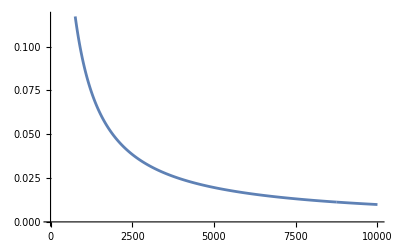

```mathematica
ListLinePlot[gg]
```

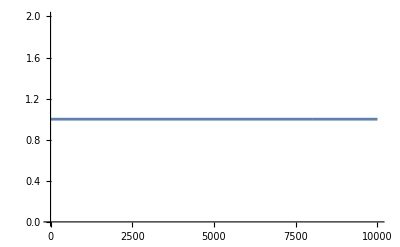

```mathematica
ListLinePlot[gg]
```

```mathematica
Exp[-ⅈ 2  π]//N
```

1.

```mathematica
5 π /4//N
```

3.92699

```mathematica
f[x_]:=Log[1+Exp[10x]]/10;
```

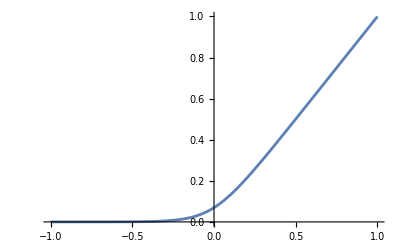

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
A0 = {{a0, a1, a2},{a1,a4, a5 }, {a2, a5, a8}};
B0 = {{b0, b1, b2 },{b1,b4, b5 }, {b2, b5, b8}};
A0i = {{0, a9, a10},{-a9,0, a11 }, {-a10, -a11, 0}};
B0i = {{0, b9, b10},{-b9,0, b11 }, {-b10, -b11, 0}};
H0 = {{h0, h1, h2 },{h1,h4, h5 }, {h2, h5, h8}};
H0i = {{0, h9, b10},{-h9,0, h11 }, {-h10, -h11, 0}};
Expand[((B0+ⅈ B0i -ⅈ (H0+ⅈ H0i)).(A0+ⅈ A0i).(B0+ⅈ B0i +ⅈ (H0+ⅈ H0i))+(B0-ⅈ B0i +ⅈ (H0-ⅈ H0i)).(A0-ⅈ A0i).(B0-ⅈ B0i -ⅈ (H0-ⅈ H0i)))/2]//MatrixForm
```

(a0 b0^2+2 a1 b0 b1+a4 b1^2+2 a10 b0 b10+a2 b0 b10+2 a11 b1 b10+a5 b1 b10+a8 b10^2+2 a2 b0 b2+2 a5 b1 b2+a8 b10 b2+a8 b2^2+2 a9 b0 b9-a11 b10 b9+2 a5 b10 b9-2 a11 b2 b9+a4 b9^2+2 a9 b1 h0+a10 b10 h0-2 a2 b10 h0+2 a10 b2 h0-2 a1 b9 h0+a0 h0^2-2 a9 b0 h1+a11 b10 h1-2 a5 b10 h1+2 a11 b2 h1-2 a4 b9 h1+2 a1 h0 h1+a4 h1^2+a2 b0 h10+a5 b1 h10+a8 b10 h10+a8 b2 h10-a11 b9 h10+a10 h0 h10+a11 h1 h10-2 a10 b0 h2-2 a11 b1 h2-2 a8 b10 h2-2 a5 b9 h2+2 a2 h0 h2+2 a5 h1 h2+a8 h2^2+2 a1 b0 h9+2 a4 b1 h9+2 a11 b10 h9+a5 b10 h9+2 a5 b2 h9+2 a9 h0 h9+a5 h10 h9-2 a11 h2 h9+a4 h9^2 | a0 b0 b1+a1 b1^2+a10 b1 b10+a2 b1 b10+a10 b0 b11+a11 b1 b11+a8 b10 b11+a2 b1 b2+a1 b0 b4+a4 b1 b4+a11 b10 b4+a5 b10 b4+a5 b2 b4+a2 b0 b5+a5 b1 b5+a8 b10 b5+a8 b2 b5+2 a9 b1 b9+a10 b10 b9-a2 b10 b9+a5 b11 b9+a10 b2 b9-a11 b5 b9-a1 b9^2-a2 b11 h0+a9 b4 h0+a10 b5 h0+a0 b9 h0+a10 b10 h1-a2 b10 h1-a5 b11 h1+a10 b2 h1+a11 b5 h1+a0 h0 h1+a1 h1^2+a2 b0 h11+a5 b1 h11+a8 b10 h11+a8 b2 h11-a11 b9 h11+a10 h0 h11+a11 h1 h11-a10 b1 h2-a8 b11 h2-a11 b4 h2+a2 b9 h2+a2 h1 h2-a9 b0 h4+a11 b10 h4-a5 b10 h4+a11 b2 h4-a4 b9 h4+a1 h0 h4+a4 h1 h4+a5 h2 h4-a10 b0 h5-a11 b1 h5-a8 b10 h5-a5 b9 h5+a2 h0 h5+a5 h1 h5+a8 h2 h5-a0 b0 h9-a10 b10 h9-a2 b10 h9+a11 b11 h9-a2 b2 h9+a4 b4 h9+a5 b5 h9+2 a9 h1 h9+a5 h11 h9+a10 h2 h9-a11 h5 h9-a1 h9^2 | -a0 b0 b10-a1 b1 b10+a9 b1 b10-2 a2 b10^2-a9 b0 b11+a11 b10 b11-a5 b10 b11+a0 b0 b2+a1 b1 b2+2 a10 b10 b2+a11 b11 b2+a2 b2^2+a1 b0 b5+a4 b1 b5+a11 b10 b5+a5 b10 b5+a5 b2 b5+a2 b0 b8+a5 b1 b8+a8 b10 b8+a8 b2 b8-a1 b10 b9-a9 b10 b9-a4 b11 b9+a9 b2 b9-a11 b8 b9+a0 b10 h0+a1 b11 h0+a9 b5 h0+a10 b8 h0+a1 b10 h1+a9 b10 h1+a4 b11 h1-a9 b2 h1+a11 b8 h1-a1 b0 h11-a4 b1 h11-a11 b10 h11-a5 b10 h11-a5 b2 h11-a9 h0 h11+a9 b1 h2+2 a10 b10 h2+a5 b11 h2-a11 b5 h2-a1 b9 h2+a0 h0 h2+a1 h1 h2+a11 h11 h2+a2 h2^2-a9 b0 h5+a11 b10 h5-a5 b10 h5+a11 b2 h5-a4 b9 h5+a1 h0 h5+a4 h1 h5+a5 h2 h5-a10 b0 h8-a11 b1 h8-a8 b10 h8-a5 b9 h8+a2 h0 h8+a5 h1 h8+a8 h2 h8-a1 b10 h9+a9 b10 h9+a1 b2 h9+a4 b5 h9+a5 b8 h9-a4 h11 h9+a9 h2 h9-a11 h8 h9
a0 b0 b1+a1 b1^2+a10 b1 b10+a10 b0 b11+a11 b1 b11+a8 b10 b11+a2 b1 b2+a1 b0 b4+a4 b1 b4+a11 b10 b4+a5 b2 b4+a2 b0 b5+a5 b1 b5+a8 b2 b5+2 a9 b1 b9-a2 b10 b9+a5 b11 b9+a10 b2 b9-a11 b5 b9-a1 b9^2-a2 b11 h0+a9 b4 h0+a10 b5 h0+a0 b9 h0-a2 b10 h1-a5 b11 h1+a10 b2 h1+a11 b5 h1+a0 h0 h1+a1 h1^2+a2 b1 h10+a5 b4 h10+a8 b5 h10+a10 b9 h10+a10 h1 h10+a2 b0 h11+a5 b1 h11+a8 b2 h11-a11 b9 h11+a10 h0 h11+a11 h1 h11+a8 h10 h11-a10 b1 h2-a8 b11 h2-a11 b4 h2+a2 b9 h2+a2 h1 h2-a9 b0 h4-a5 b10 h4+a11 b2 h4-a4 b9 h4+a1 h0 h4+a4 h1 h4+a11 h10 h4+a5 h2 h4-a10 b0 h5-a11 b1 h5-a8 b10 h5-a5 b9 h5+a2 h0 h5+a5 h1 h5+a8 h2 h5-a0 b0 h9-a10 b10 h9+a11 b11 h9-a2 b2 h9+a4 b4 h9+a5 b5 h9+2 a9 h1 h9-a2 h10 h9+a5 h11 h9+a10 h2 h9-a11 h5 h9-a1 h9^2 | a0 b1^2+2 a10 b1 b11+a8 b11^2+2 a1 b1 b4+2 a11 b11 b4+a4 b4^2+2 a2 b1 b5+2 a5 b4 b5+a8 b5^2-2 a2 b11 b9+2 a9 b4 b9+2 a10 b5 b9+a0 b9^2-2 a2 b11 h1+2 a9 b4 h1+2 a10 b5 h1+2 a0 b9 h1+a0 h1^2+2 a2 b1 h11+2 a5 b4 h11+2 a8 b5 h11+2 a10 b9 h11+2 a10 h1 h11+a8 h11^2-2 a9 b1 h4-2 a5 b11 h4+2 a11 b5 h4+2 a1 b9 h4+2 a1 h1 h4+2 a11 h11 h4+a4 h4^2-2 a10 b1 h5-2 a8 b11 h5-2 a11 b4 h5+2 a2 b9 h5+2 a2 h1 h5+2 a5 h4 h5+a8 h5^2-2 a0 b1 h9-2 a10 b11 h9-2 a1 b4 h9-2 a2 b5 h9-2 a2 h11 h9+2 a9 h4 h9+2 a10 h5 h9+a0 h9^2 | -a0 b1 b10-a9 b1 b11-a10 b10 b11-a2 b10 b11-a5 b11^2+a0 b1 b2+a10 b11 b2-a1 b10 b4+a9 b10 b4+a1 b2 b4+a1 b1 b5+a10 b10 b5-a2 b10 b5+2 a11 b11 b5+a2 b2 b5+a4 b4 b5+a5 b5^2+a2 b1 b8+a5 b4 b8+a8 b5 b8+a0 b10 b9+a1 b11 b9+a9 b5 b9+a10 b8 b9+a0 b10 h1+a1 b11 h1+a9 b5 h1+a10 b8 h1-a1 b1 h11+a10 b10 h11-a2 b10 h11+a2 b2 h11-a4 b4 h11+a8 b8 h11-a9 b9 h11-a9 h1 h11-a5 h11^2-a2 b11 h2+a9 b4 h2+a10 b5 h2+a0 b9 h2+a0 h1 h2+a10 h11 h2+a1 b10 h4+a9 b10 h4+a4 b11 h4-a9 b2 h4+a11 b8 h4+a1 h2 h4-a9 b1 h5+a10 b10 h5+a2 b10 h5-a10 b2 h5+a1 b9 h5+a1 h1 h5+2 a11 h11 h5+a2 h2 h5+a4 h4 h5+a5 h5^2-a10 b1 h8-a8 b11 h8-a11 b4 h8+a2 b9 h8+a2 h1 h8+a5 h4 h8+a8 h5 h8+a0 b10 h9+a9 b11 h9-a0 b2 h9-a1 b5 h9-a2 b8 h9+a1 h11 h9+a9 h5 h9+a10 h8 h9
a9 b1 b10-a2 b10^2-a9 b0 b11-a5 b10 b11+a0 b0 b2+a1 b1 b2+2 a10 b10 b2+a11 b11 b2+a2 b2^2+a1 b0 b5+a4 b1 b5+a11 b10 b5+a5 b2 b5+a2 b0 b8+a5 b1 b8+a8 b2 b8-a1 b10 b9-a4 b11 b9+a9 b2 b9-a11 b8 b9+a0 b10 h0+a1 b11 h0+a9 b5 h0+a10 b8 h0+a1 b10 h1+a4 b11 h1-a9 b2 h1+a11 b8 h1-a0 b0 h10-a1 b1 h10+a11 b11 h10+a5 b5 h10+a8 b8 h10-a9 b9 h10+a9 h1 h10-a2 h10^2-a1 b0 h11-a4 b1 h11-a11 b10 h11-a5 b2 h11-a9 h0 h11-a5 h10 h11+a9 b1 h2+a5 b11 h2-a11 b5 h2-a1 b9 h2+a0 h0 h2+a1 h1 h2+2 a10 h10 h2+a11 h11 h2+a2 h2^2-a9 b0 h5-a5 b10 h5+a11 b2 h5-a4 b9 h5+a1 h0 h5+a4 h1 h5+a11 h10 h5+a5 h2 h5-a10 b0 h8-a11 b1 h8-a8 b10 h8-a5 b9 h8+a2 h0 h8+a5 h1 h8+a8 h2 h8+a9 b10 h9+a1 b2 h9+a4 b5 h9+a5 b8 h9-a1 h10 h9-a4 h11 h9+a9 h2 h9-a11 h8 h9 | -a9 b1 b11-a2 b10 b11-a5 b11^2+a0 b1 b2+a10 b11 b2+a9 b10 b4+a1 b2 b4+a1 b1 b5+a10 b10 b5+2 a11 b11 b5+a2 b2 b5+a4 b4 b5+a5 b5^2+a2 b1 b8+a5 b4 b8+a8 b5 b8+a0 b10 b9+a1 b11 b9+a9 b5 b9+a10 b8 b9+a0 b10 h1+a1 b11 h1+a9 b5 h1+a10 b8 h1-a0 b1 h10-a10 b11 h10-a1 b4 h10-a2 b5 h10-a1 b1 h11+a10 b10 h11+a2 b2 h11-a4 b4 h11+a8 b8 h11-a9 b9 h11-a9 h1 h11-a2 h10 h11-a5 h11^2-a2 b11 h2+a9 b4 h2+a10 b5 h2+a0 b9 h2+a0 h1 h2+a10 h11 h2+a1 b10 h4+a4 b11 h4-a9 b2 h4+a11 b8 h4+a9 h10 h4+a1 h2 h4-a9 b1 h5+a2 b10 h5-a10 b2 h5+a1 b9 h5+a1 h1 h5+a10 h10 h5+2 a11 h11 h5+a2 h2 h5+a4 h4 h5+a5 h5^2-a10 b1 h8-a8 b11 h8-a11 b4 h8+a2 b9 h8+a2 h1 h8+a5 h4 h8+a8 h5 h8+a9 b11 h9-a0 b2 h9-a1 b5 h9-a2 b8 h9+a0 h10 h9+a1 h11 h9+a9 h5 h9+a10 h8 h9 | a0 b10^2+2 a1 b10 b11+a9 b10 b11+a4 b11^2-a0 b10 b2-2 a9 b11 b2+a0 b2^2-a1 b10 b5+2 a9 b10 b5+2 a1 b2 b5+a4 b5^2+2 a10 b10 b8-a2 b10 b8+2 a11 b11 b8+2 a2 b2 b8+2 a5 b5 b8+a8 b8^2+a0 b10 h10+a9 b11 h10-a0 b2 h10-a1 b5 h10-a2 b8 h10+a1 b10 h11-2 a9 b10 h11-2 a1 b2 h11-2 a4 b5 h11-2 a5 b8 h11+a1 h10 h11+a4 h11^2+2 a0 b10 h2+2 a1 b11 h2+2 a9 b5 h2+2 a10 b8 h2-2 a9 h11 h2+a0 h2^2+2 a1 b10 h5+a9 b10 h5+2 a4 b11 h5-2 a9 b2 h5+2 a11 b8 h5+a9 h10 h5+2 a1 h2 h5+a4 h5^2+a10 b10 h8+2 a2 b10 h8+2 a5 b11 h8-2 a10 b2 h8-2 a11 b5 h8+a10 h10 h8+2 a11 h11 h8+2 a2 h2 h8+2 a5 h5 h8+a8 h8^2)

```mathematica
UpperTriangularize[Expand[(B0.A0.B0)]]//MatrixForm
```

(a0 b0^2+2 a1 b0 b1+a4 b1^2+2 a2 b0 b2+2 a5 b1 b2+a8 b2^2 | a0 b0 b1+a1 b1^2+a2 b1 b2+a1 b0 b4+a4 b1 b4+a5 b2 b4+a2 b0 b5+a5 b1 b5+a8 b2 b5 | a0 b0 b2+a1 b1 b2+a2 b2^2+a1 b0 b5+a4 b1 b5+a5 b2 b5+a2 b0 b8+a5 b1 b8+a8 b2 b8
0 | a0 b1^2+2 a1 b1 b4+a4 b4^2+2 a2 b1 b5+2 a5 b4 b5+a8 b5^2 | a0 b1 b2+a1 b2 b4+a1 b1 b5+a2 b2 b5+a4 b4 b5+a5 b5^2+a2 b1 b8+a5 b4 b8+a8 b5 b8
0 | 0 | a0 b2^2+2 a1 b2 b5+a4 b5^2+2 a2 b2 b8+2 a5 b5 b8+a8 b8^2)

```mathematica
BBv = {b0^2, 2b0 b1, 2b0 b2, b1^2, 2b1 b2, b2^2}
```

{b0^2,2 b0 b1,2 b0 b2,b1^2,2 b1 b2,b2^2}

```mathematica
B0.B0//MatrixForm
```

(b0^2+b1^2+b2^2 | b0 b1+b1 b4+b2 b5 | b0 b2+b1 b5+b2 b8
b0 b1+b1 b4+b2 b5 | b1^2+b4^2+b5^2 | b1 b2+b4 b5+b5 b8
b0 b2+b1 b5+b2 b8 | b1 b2+b4 b5+b5 b8 | b2^2+b5^2+b8^2)

```mathematica
ABv = {{a0 b0+a1 b1+a2 b2, a0 b1+a1 b4+a2 b5,  a0 b2+a1 b5+a2 b8, a1 b1+a4 b4+a5 b5, a1 b2+a4 b5+a5 b8, a2 b2+a5 b5+a8 b8}}
```

{{a0 b0+a1 b1+a2 b2,a0 b1+a1 b4+a2 b5,a0 b2+a1 b5+a2 b8,a1 b1+a4 b4+a5 b5,a1 b2+a4 b5+a5 b8,a2 b2+a5 b5+a8 b8}}

```mathematica
A0//MatrixForm
B0//MatrixForm
```

(a0 | a1 | a2
a1 | a4 | a5
a2 | a5 | a8)

(b0 | b1 | b2
b1 | b4 | b5
b2 | b5 | b8)

```mathematica
A0v = {a0, a1, a2, a4, a5, a8};
B0v = {b0, b1, b2, b4, b5, b8};
```

```mathematica
A0v*B0v
```

{a0 b0,a1 b1,a2 b2,a4 b4,a5 b5,a8 b8}

```mathematica
KroneckerProduct[B0v, B0v].A0v
```

{a0 b0^2+a1 b0 b1+a2 b0 b2+a4 b0 b4+a5 b0 b5+a8 b0 b8,a0 b0 b1+a1 b1^2+a2 b1 b2+a4 b1 b4+a5 b1 b5+a8 b1 b8,a0 b0 b2+a1 b1 b2+a2 b2^2+a4 b2 b4+a5 b2 b5+a8 b2 b8,a0 b0 b4+a1 b1 b4+a2 b2 b4+a4 b4^2+a5 b4 b5+a8 b4 b8,a0 b0 b5+a1 b1 b5+a2 b2 b5+a4 b4 b5+a5 b5^2+a8 b5 b8,a0 b0 b8+a1 b1 b8+a2 b2 b8+a4 b4 b8+a5 b5 b8+a8 b8^2}

```mathematica
A0.B0//MatrixForm
```

(a0 b0+a1 b1+a2 b2 | a0 b1+a1 b4+a2 b5 | a0 b2+a1 b5+a2 b8
a1 b0+a4 b1+a5 b2 | a1 b1+a4 b4+a5 b5 | a1 b2+a4 b5+a5 b8
a2 b0+a5 b1+a8 b2 | a2 b1+a5 b4+a8 b5 | a2 b2+a5 b5+a8 b8)